# Recognizing shapes

```mathematica
randomRectangle:=Translate[Rectangle[{-.5,-.5},{.5,.5}],
RandomReal[{-1,1},2]]
```

```mathematica
randomDisk:=Translate[Disk[{0,0},.5],RandomReal[{-1,1},2]]
```

```mathematica
randomPentagon:=Translate[RegularPolygon[0.6,5],RandomReal[{-1,1},2]]
```

```mathematica
randomHexagon:=Translate[RegularPolygon[0.6,6],RandomReal[{-1,1},2]]
```

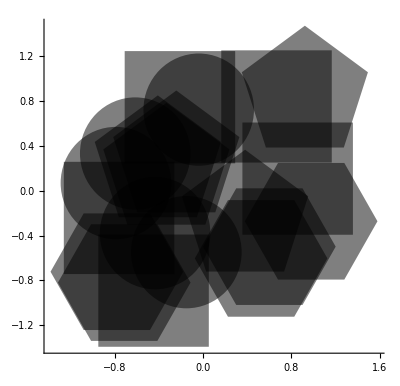

```mathematica
Graphics[{Opacity[.5],Table[randomRectangle,5],Table[randomDisk,5],Table[randomPentagon,5],Table[randomHexagon,5]},PlotRange->2,Axes->True]
```

```mathematica
r=RandomInteger[{0,2}]
```

2

```mathematica
Switch[r,0,"zero",1,"one",2,"two"]
```

two

```mathematica
randomExample[n_]:=Module[{r,p,g,i},
Table[
r=RandomInteger[{0,3}];
p=Switch[r,0,randomDisk,1,randomRectangle,2,randomPentagon,3,randomHexagon];
g=Graphics[{Black,p},PlotRange->1,Background->White];
i=Image[g,ImageSize->{100,100}];
i->Switch[r,0,"Disk",1,"Rectangle",2,"Pentagon",3,"Hexagon"]
,n]
]
```

```mathematica
randomExample[10]
```

{-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Hexagon,-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Pentagon,-Graphics-→Disk,-Graphics-→Hexagon,-Graphics-→Pentagon,-Graphics-→Rectangle}

```mathematica
training=randomExample[3000];
```

```mathematica
RandomSample[training,10]
```

{-Graphics-→Pentagon,-Graphics-→Pentagon,-Graphics-→Pentagon,-Graphics-→Rectangle,-Graphics-→Pentagon,-Graphics-→Rectangle,-Graphics-→Rectangle,-Graphics-→Rectangle,-Graphics-→Pentagon,-Graphics-→Pentagon}

```mathematica
(* old code *)
net=NetGraph[{
ConvolutionLayer[20,{4,4}],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[30,{4,4}],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
DotPlusLayer[100],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
{1->2->3->4->5->6->7->8->9->10->11},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"Disk","Rectangle","Pentagon"}}]
];
```

```mathematica
(* new code *)
net=NetGraph[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],
PoolingLayer[8,8],
FlattenLayer[],
DotPlusLayer[4],
SoftmaxLayer[]
},
{1->2->3->4->5->6->7},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"Disk","Rectangle","Pentagon","Hexagon"}}]
]
```

NetGraph[]

```mathematica
net=NetInitialize[net];
```

```mathematica
net[-Graphics-]
```

Disk

```mathematica
result=NetTrain[net,training,
TargetDevice->"GPU",
MaxTrainingRounds->120,Method->{"ADAM","InitialLearningRate"->0.005}]
```

NetGraph[]

```mathematica
result[-Graphics-,"Probabilities"]
```

<|Disk→0.425976,Rectangle→0.00157446,Polygon→0.57245|>

```mathematica
validation=randomExample[100];
```

```mathematica
Length[validation]
```

100

```mathematica
RandomSample[validation,5]
```

{-Graphics-→Pentagon,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Pentagon,-Graphics-→Disk}

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.8

```mathematica
cm["Accuracy"]
```

0.83

```mathematica
cm["Accuracy"]
```

0.78

```mathematica
cm["Accuracy"]
```

1.

```mathematica
cm["Accuracy"]
```

0.93

```mathematica
cm["Accuracy"]
```

1.

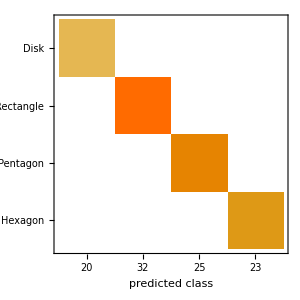

```mathematica
cm["ConfusionMatrixPlot"]
```